{50,1}

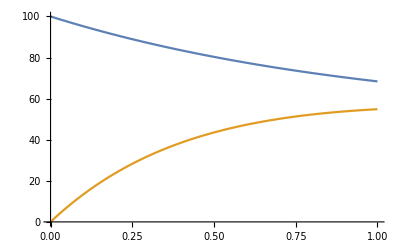

{{88.94},{7938.62},{28.287}}

```mathematica
ClearAll["Global`*"]
(*0 -> A, A -> 0*)
(*NOTE: x*x ≠ xsq*)

c = {50, 1}
eqns={x'[t]==c[[1]]-c[[2]]x[t],
xsq'[t]==-2c[[2]]xsq[t]+2c[[1]]x[t]+c[[1]]+c[[2]]x[t],
x[0]==100,xsq[0]==100^2};
sol=DSolve[eqns,{x,xsq},t];
Plot[{x[t]/.sol,xsq[t]-x[t]^2/.sol},{t,0,1}]
N[{x[t]/.sol,xsq[t]/.sol,xsq[t]-x[t]^2/.sol}/.{t->0.25},12]
```